# RandomCustomGraph

One-line description explaining the function’s basic purpose

## Definition

```mathematica
RandomCustomGraph[{nodes_,edges_},quality_]:=NestWhile[RandomGraph[{nodes,edges}]&,Null,!quality[#]&,1,1000]
```

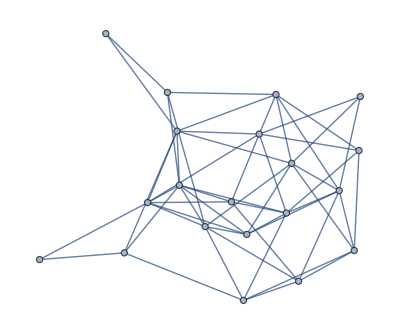

```mathematica
RandomCustomGraph[{20,54},ConnectedGraphQ]
```

```mathematica
ConnectedGraphQ[RandomCustomGraph[{20,54},ConnectedGraphQ]]
```

True

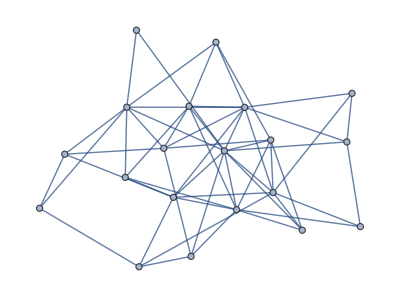

```mathematica
RandomCustomGraph[{20,54},PlanarGraphQ]
```

```mathematica
RandomCustomGraph[{10,20},ConnectedGraphQ]
```

$Aborted

```mathematica
2+2
```

4

```mathematica
NestWhile[RandomGraph[{20,}],Null,!ConnectedGraphQ[#]&]
```

$Aborted

```mathematica
NestWhile[RandomMixedGraph[{8,10},0.4 ,VertexLabels->"Name"],Null,!ConnectedGraphQ[#]&]
```

$Aborted

## Documentation

### Usage

MyFunction[arg]

explanation of what use of the argument arg does.

### Details & Options

Additional information about usage and options.

## Examples

### Basic Examples

Text about the example:

```mathematica
MyFunction[x,y]
```

x y

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Author Name

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SymbolName (documented Wolfram Language symbol)

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.